# 自编码器@Phoneid

## DataPrepare

```mathematica
data=Partition[BinaryReadList["https://wolfr.am/m6DMp7U1","Real32"],lenParts={1+12+43}];
```

```mathematica
data//Length
```

4238

```mathematica
id=Import["/Users/hypergroups/Downloads/phone_id.csv","Table"];
```

```mathematica
labels=id[[All,2]]
```

{aa,ae,ae,aa,aa,ae,ah,aa,ae,aa,ae,aa,aa,ah,ae,ah,ae,aa,aa,ae,aa,ah,ah,ah,ae,ae,aa,ae,ah,ah,aa,aa,ah,aa,aa,ah,aa,ah,ah,ah,ae,ae,ae,ah,aa,ah,aa,ah,aa,aa,aa,ae,ae,ae,aa,ae,aa,ah,aa,aa,ah,aa,aa,ah,ah,ae,aa,ae,aa,aa,ah,ah,aa,aa,aa,ah,ah,aa,ah,ah,ae,ae,ae,ah,ae,ae,ah,ah,ae,ae,aa,ah,ae,ah,aa,ah,ae,aa,ah,aa,ah,ae,ah,ae,aa,ae,ae,ae,ae,aa,aa,ah,ae,aa,ah,aa,ae,ah,ah,ae,aa,ah,ae,ah,ah,ah,ae,ae,ae,ah,ae,ae,aa,ah,aa,ah,aa,ae,ae,aa,ah,ae,ah,ae,aa,aa,ae,ae,ah,ah,ah,ae,ae,aa,ae,ae,ae,ah,aa,ah,aa,ae,ah,aa,ae,ae,aa,ah,ah,ah,ah,aa,ae,aa,ah,aa,aa,ae,ah,aa}

```mathematica
lengthSample=id//Length
```

180

```mathematica
sampleData=data[[1;;lengthSample]]
```

```mathematica
trainingSamples=Thread[sampleData->labels];
```

```mathematica
sampleAsso=GroupBy[trainingSamples,Last->First];
```

```mathematica
sampleMean=Mean/@sampleAsso
```

<|aa→{2.4,0.05,0.2,0.533333,0.1,0.116667,0.0206835,0.0399942,0.464341,0.535659,0.50911,0.49089,0.425765,0.844966,0.700878,0.421214,0.443633,0.543463,0.503021,0.677674,0.523453,0.468589,0.529715,0.490707,0.365145,0.327706,0.410747,0.476659,0.573177,0.558261,0.536609,0.526819,0.470756,0.493537,0.498011,0.49236,0.575101,0.529315,0.521721,0.348482,0.472007,0.481688,0.474576,0.483775,0.524546,0.492768,0.506751,0.477194,0.513138,0.51302,0.512593,0.501025,0.535492,0.431226,0.323826,0.983333},ae→{2.73333,0.1,0.216667,0.483333,0.116667,0.0833333,0.0190048,0.0384526,0.553092,0.446908,0.505825,0.494175,0.412888,0.840692,0.705544,0.417389,0.437232,0.51795,0.50416,0.685744,0.526418,0.466531,0.507235,0.507089,0.357549,0.327416,0.413366,0.477812,0.563347,0.559673,0.536127,0.5214,0.470425,0.50535,0.49674,0.494725,0.576221,0.520288,0.519435,0.345952,0.4689,0.475071,0.471113,0.490926,0.539623,0.492398,0.511724,0.481035,0.520041,0.512078,0.504648,0.502907,0.545222,0.431007,0.324346,0.933333},ah→{2.81667,0.1,0.133333,0.516667,0.1,0.15,0.0190647,0.0387435,0.424234,0.575766,0.493398,0.506602,0.407658,0.827507,0.709268,0.421979,0.463939,0.54334,0.491801,0.683701,0.498934,0.47341,0.531199,0.48379,0.366306,0.342504,0.416255,0.479532,0.569944,0.557411,0.518315,0.533176,0.47038,0.510469,0.500086,0.483201,0.597468,0.517748,0.519804,0.34809,0.468678,0.477106,0.47132,0.498042,0.523671,0.490696,0.515189,0.479341,0.518931,0.510974,0.503635,0.50939,0.549046,0.430957,0.325058,0.95}|>

```mathematica
nf=Nearest[sampleMean]
```

NearestFunction[…]

```mathematica
Table[nf[sampleData[[i]]]->labels[[i]],{i,180}]
```

{{aa}→aa,{aa}→ae,{aa}→ae,{aa}→aa,{aa}→aa,{aa}→ae,{aa}→ah,{aa}→aa,{aa}→ae,{aa}→aa,{aa}→ae,{aa}→aa,{aa}→aa,{aa}→ah,{aa}→ae,{aa}→ah,{aa}→ae,{aa}→aa,{aa}→aa,{aa}→ae,{aa}→aa,{aa}→ah,{aa}→ah,{aa}→ah,{aa}→ae,{aa}→ae,{aa}→aa,{aa}→ae,{aa}→ah,{aa}→ah,{aa}→aa,{aa}→aa,{aa}→ah,{aa}→aa,{aa}→aa,{aa}→ah,{aa}→aa,{aa}→ah,{aa}→ah,{aa}→ah,{aa}→ae,{aa}→ae,{aa}→ae,{aa}→ah,{aa}→aa,{aa}→ah,{aa}→aa,{aa}→ah,{aa}→aa,{aa}→aa,{aa}→aa,{aa}→ae,{aa}→ae,{aa}→ae,{aa}→aa,{aa}→ae,{aa}→aa,{aa}→ah,{aa}→aa,{aa}→aa,{aa}→ah,{aa}→aa,{aa}→aa,{aa}→ah,{aa}→ah,{aa}→ae,{aa}→aa,{aa}→ae,{aa}→aa,{aa}→aa,{aa}→ah,{aa}→ah,{aa}→aa,{aa}→aa,{aa}→aa,{aa}→ah,{aa}→ah,{aa}→aa,{aa}→ah,{aa}→ah,{aa}→ae,{aa}→ae,{aa}→ae,{aa}→ah,{aa}→ae,{aa}→ae,{aa}→ah,{aa}→ah,{aa}→ae,{ah}→ae,{ah}→aa,{ae}→ah,{ah}→ae,{ae}→ah,{ah}→aa,{ah}→ah,{ah}→ae,{ah}→aa,{ae}→ah,{ae}→aa,{ah}→ah,{ah}→ae,{ah}→ah,{ae}→ae,{ae}→aa,{ae}→ae,{ae}→ae,{ae}→ae,{ae}→ae,{ae}→aa,{ah}→aa,{ah}→ah,{ae}→ae,{ah}→aa,{ah}→ah,{ah}→aa,{ah}→ae,{ah}→ah,{ah}→ah,{ah}→ae,{ah}→aa,{ah}→ah,{ah}→ae,{ah}→ah,{ah}→ah,{ah}→ah,{ah}→ae,{ah}→ae,{ah}→ae,{ah}→ah,{ah}→ae,{ae}→ae,{ah}→aa,{ah}→ah,{ah}→aa,{ah}→ah,{ae}→aa,{ae}→ae,{ae}→ae,{ae}→aa,{ah}→ah,{ae}→ae,{ah}→ah,{ah}→ae,{ah}→aa,{ah}→aa,{ah}→ae,{ah}→ae,{ah}→ah,{ah}→ah,{ah}→ah,{ah}→ae,{ah}→ae,{ah}→aa,{ah}→ae,{ah}→ae,{ah}→ae,{ah}→ah,{ah}→aa,{ah}→ah,{ah}→aa,{ah}→ae,{ah}→ah,{ah}→aa,{ah}→ae,{ah}→ae,{ah}→aa,{ah}→ah,{ah}→ah,{ah}→ah,{ah}→ah,{ah}→aa,{ah}→ae,{ah}→aa,{ah}→ah,{ah}→aa,{ah}→aa,{ah}→ae,{ah}→ah,{ah}→aa}

```mathematica
net=NetGraph[{FlattenLayer[],2,Ramp,56,Tanh,ReshapeLayer[{56}],MeanSquaredLossLayer[]},{1->2->3->4->5->6->NetPort["Output"],6->NetPort[7,"Input"],NetPort["Input"]->NetPort[7,"Target"]},"Input"->{56},
"Output"->{56}]
```

NetGraph[<>]

### CheckLoss

```mathematica
meanSquaredLoss=N[Mean[Flatten[(#Input-#Target)^2]]]&;
```

```mathematica
trained=NetTrain[net,<|"Input"->sampleData|>];
```

## 降维@可视化

```mathematica
reconstructor=Take[trained,{NetPort["Input"],NetPort["Output"]}]
```

NetGraph[<>]

```mathematica
encoder=Take[trained,{NetPort["Input"],2}]
```

NetGraph[<>]

```mathematica
testSubset=asso;
testData=Keys[testSubset];
features=encoder[testData];
```

```mathematica
classes=Values[testSubset];
```

```mathematica
coords2D=DimensionReduce[features,2,Method->"TSNE"];
```

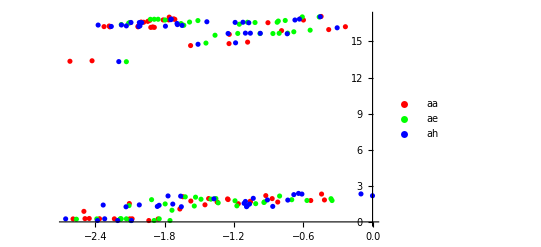

```mathematica
ListPlot[GroupBy[Thread[labels->features],First->Last],PlotStyle->{Red,Green,Blue}]
```

```mathematica
features[[1]]//Length
```

2

#### TSNE直接从784维向量聚类的效果

```mathematica
coords2D=DimensionReduce[sampleData,2,Method->"TSNE"];
```

```mathematica
coords3D=DimensionReduce[sampleData,3,Method->"TSNE"];
```

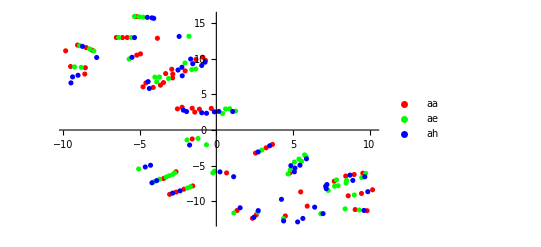

```mathematica
ListPlot[GroupBy[Thread[labels->coords2D],First->Last],PlotStyle->{Red,Green,Blue},PlotRange->Full]
```